```mathematica
Clear[SEIQRModel];
Import["https://raw.githubusercontent.com/palaciowagner/SystemModeling/master/Projects/Monkeypox/SEIQREpidemiologyModel.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModelModifications.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/WL/SystemDynamicsInteractiveInterfacesFunctions.m"];
```

```mathematica
Clear[modelSEIQR];
modelSEIQR=SEIQRModel[t,"InitialConditions"->True,"RateRules"->True,"TotalPopulationRepresentation"->"Constant"];
ModelGridTableForm[modelSEIQR]
```

<|Stocks→# | Symbol | Description
1 | NP[t] | Total Population
2 | SP[t] | Susceptible Population
3 | EP[t] | Exposed Population
4 | IP[t] | Infected Population
5 | QP[t] | Quarantined Population
6 | RP[t] | Recovered Population,Rates→# | Symbol | Description
1 | β | Contact rate for the infected population
2 | α1 | Proportion of Exposed to Infected Rate (Confirmed)
3 | α2 | Proportion Sent to Quarantine (Suspected)
4 | φ | Proportion of not detected after medical diagnosis (Discarded)
5 | τ | Proportion from Suspected to Recovered class
6 | γ | Recovery Rate
7 | 13 | Average Incubation Period
8 | λ | Average Infection Period,Equations→# | Equation
1 | SP'[t]==φ QP[t]-(β IP[t] SP[t])/NP[0]
2 | EP'[t]==-((α1+α2) EP[t])+(β IP[t] SP[t])/NP[0]
3 | IP'[t]==α1 EP[t]-γ IP[t]
4 | QP'[t]==α2 EP[t]-(τ+φ) QP[t]
5 | RP'[t]==γ IP[t]+τ QP[t],RateRules→# | Symbol | Value
1 | NP[0] | 100000
2 | β | 6.×10^-6
3 | α1 | 1/13
4 | α2 | 0.2
5 | φ | 0.2
6 | τ | 1/13+1/λ
7 | γ | 1/λ
8 | 13 | 13
9 | λ | 31/4,InitialConditions→# | Equation
1 | SP[0]==99999
2 | EP[0]==0
3 | IP[0]==1
4 | QP[0]==0
5 | RP[0]==0|>

### Getting Data

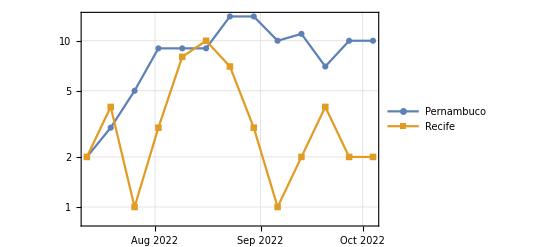

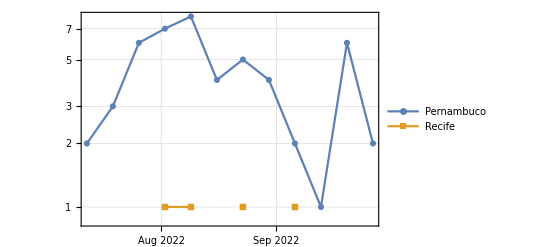

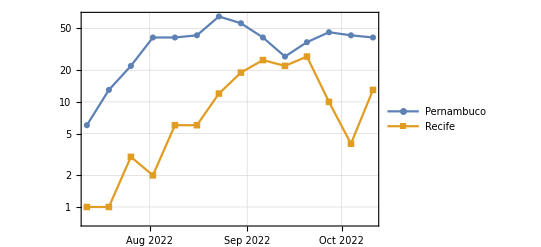

-Graphics-

```mathematica
cievsPEData := Import["https://raw.githubusercontent.com/palaciowagner/SystemModeling/master/Projects/Monkeypox/data/Pernambuco/Monkeypox%20-%20Pernambuco.csv", "Dataset", "HeaderLines" -> 1];
cievsRECData := Import["https://raw.githubusercontent.com/palaciowagner/SystemModeling/master/Projects/Monkeypox/data/Recife/Monkeypox%20-%20Recife.csv", "Dataset", "HeaderLines" -> 1];
dateFormat = {"Day", "/", "Month", "/", "Year"};
PEdataMap =cievsPEData // Normal;
RECdataMap = cievsRECData // Normal;
pernambucoPopulation =  QuantityMagnitude[EntityValue[Entity["AdministrativeDivision",{"Pernambuco","Brazil"}],"Population"]];
recifePopulation =  QuantityMagnitude[EntityValue[Entity["City",{"Recife","Pernambuco","Brazil"}],"Population"]];
(*cievsPEData*)
Clear[Smooth];
Smooth[data_] := MovingMap[Median, data,{{7,"Day"},Left,"Week"}];
totalConfirmadosPE = Ceiling[Smooth[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Confirmados"}&,PEdataMap]]]];
totalConfirmadosREC = Ceiling[Smooth[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Confirmados"}&,RECdataMap]]]];
DateListLogPlot[Tooltip[{totalConfirmadosPE, totalConfirmadosREC} ], Joined->True, PlotLegends->{"Pernambuco", "Recife"}, PlotMarkers->Automatic, GridLines -> Automatic]

totalProvaveisPE = Ceiling[Smooth[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Prováveis"}&,PEdataMap]]]];
totalProvaveisREC = Ceiling[Smooth[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Prováveis"}&,RECdataMap]]]];
DateListLogPlot[Tooltip[{totalProvaveisPE, totalProvaveisREC} ], Joined->True, PlotLegends->{"Pernambuco", "Recife"}, PlotMarkers->Automatic, GridLines -> Automatic]

totalSuspeitosPE = Ceiling[Smooth[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Suspeitos"}&,PEdataMap]]]];
totalSuspeitosREC = Ceiling[Smooth[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Suspeitos"}&,RECdataMap]]]];
DateListLogPlot[Tooltip[{totalSuspeitosPE, totalSuspeitosREC} ], Joined->True, PlotLegends->{"Pernambuco", "Recife"}, PlotMarkers->Automatic, GridLines -> Automatic]

totalNotificadosPE= Ceiling[Smooth[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Notificados"}&,PEdataMap]]]];
totalNotificadosREC= Ceiling[Smooth[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Notificados"}&,RECdataMap]]]];
DateListLogPlot[Tooltip[{totalSuspeitosPE, totalSuspeitosREC} ], Joined->True, PlotLegends->{"Pernambuco", "Recife"}, PlotMarkers->Automatic, GridLines -> Automatic]
```

## Dados Literatura

Alguns dados que tirei de alguns artigos sobre a dinâmica da Monkeypox que serão uteis para as formulas

### Período de Incubação [1]

```mathematica
incubation = Range[5,21];
avgIncubation = Mean[incubation];
ζ = avgIncubation
```

13

### Período de Infecção [1]

```mathematica
prodomalPhase = Range[0,3];
rashPhase = Range[7,21];
avgTotalInfection = Mean[Map[Mean] @ {prodomalPhase, rashPhase}];
δ = avgTotalInfection
```

31/4

### Taxa de Recuperação (γ)

De acordo com [2], γ ==1/δ, sendo δ a média do período de infecção total.

```mathematica
initialInfected =  Normal[totalConfirmadosPE][[1]][[2]];
initialExposed = Normal[totalProvaveisPE][[1]][[2]];
initialQuarantine = Normal[totalSuspeitosPE][[1]][[2]];
lsFocusParams={β, α1, α2};

modelSEIQR=SetRateRules[modelSEIQR,<|NP[0]->pernambucoPopulation|>];
modelSEIQR=SetInitialConditions[modelSEIQR,
<|SP[0]->pernambucoPopulation-initialInfected,
EP[0]-> initialExposed,
IP[0]-> initialInfected,
QP[0]->initialQuarantine
|>]; (* Subtrair do número da primeira semana epidemiológica*)
lsActualEquations=Join[modelSEIQR["Equations"]//.KeyDrop[modelSEIQR["RateRules"],lsFocusParams],modelSEIQR["InitialConditions"]];
ResourceFunction["GridTableForm"][List/@lsActualEquations]
```

# | 1
1 | SP'[t]==0.2 QP[t]-(β IP[t] SP[t])/8931028
2 | EP'[t]==-((α1+α2) EP[t])+(β IP[t] SP[t])/8931028
3 | IP'[t]==α1 EP[t]-(4 IP[t])/31
4 | QP'[t]==α2 EP[t]-0.405955 QP[t]
5 | RP'[t]==(4 IP[t])/31+(83 QP[t])/403
6 | SP[0]==8931026
7 | EP[0]==2
8 | IP[0]==2
9 | QP[0]==6
10 | RP[0]==0

```mathematica
aSol=Association@Flatten@ParametricNDSolve[lsActualEquations,Head/@Keys[modelSEIQR["Stocks"]],{t,0,20},lsFocusParams]
```

<|NP→ParametricFunction[<>],SP→ParametricFunction[<>],EP→ParametricFunction[<>],IP→ParametricFunction[<>],QP→ParametricFunction[<>],RP→ParametricFunction[<>]|>

```mathematica
opts={PlotRange->All,PlotLegends->None,PlotTheme->"Detailed",PerformanceGoal->"Speed",ImageSize->600};
lsPopulationKeys=GetPopulationSymbols[modelSEIQR,__~~"Population"];
Manipulate[DynamicModule[{lsPopulationPlots},lsPopulationPlots=ParametricSolutionsPlots[modelSEIQR["Stocks"],KeyTake[aSol,lsPopulationKeys],{contactRate,expToInfected,suspected},nWeeks,"LogPlot"->popLogPlotQ,"Together"->popTogetherQ,"Derivatives"->popDerivativesQ,"DerivativePrefix"->"Δ",opts];
Multicolumn[lsPopulationPlots,nPlotColumns,Dividers->All,FrameStyle->GrayLevel[0.8]]],{{contactRate,6*10^-6,"Contact rate of the infected population"},10^-6,9*10^-6,10^-6,Appearance->{"Open"}},{{expToInfected,2*10^-2,"Exposed to infection Rate"},10^-2,9*10^-2,10^-2,Appearance->{"Open"}},{{suspected,2*10^-1,"Suspected Rate"},10^-1,9*10^-1,10^-1,Appearance->{"Open"}},{{nWeeks,2,"Epidemiological Week"},1,20,1,Appearance->{"Open"}},{{popTogetherQ,True,"Plot populations together"},{False,True}},{{popDerivativesQ,False,"Plot populations derivatives"},{False,True}},{{popLogPlotQ,False,"LogPlot populations"},{False,True}},{{nPlotColumns,1,"Number of plot columns"},Range[5]},ControlPlacement->Left,ContinuousAction->False]
```